# Gráficos procedurales estilo 8-bit

## Fondos pixelados

Pixelado simple

```mathematica
HorizontalLine[color_,length_]:=ConstantArray[color,length];
SimpleBackground[color1_,color2_,size_,delta_]:= Module[{tbl,step},
step = 1/size;
tbl = Table[HorizontalLine[Blend[{color1,color2},Round[h,delta]],size],{h,0,1,step}];
Return[ArrayPlot[tbl,Frame->False]];
];
```

```mathematica
SimpleBackground[ColorData["Atoms"]["N"],ColorData["Atoms"]["Cr"],100,0.1]
```

Patrón periódico

```mathematica
CalculateColor[color1_,color2_,h_,colorInterval_]:= Blend[{color1,color2},Round[h,colorInterval]];
PatternHorizontalLine[currentcolor_,nextcolor_,noise_,length_,phase_:0]:=Module[{line},
line = ConstantArray[currentcolor,length];
Part[line,Span[1+phase,-1,noise]] = nextcolor;
Return[line]; 
];
CreatePeriodicBackground[color1_,color2_,l_,h_,colorInterval_,noise_]:=Module[{Δh,colors},
Δh = 1/h;
colors = Table[
PatternHorizontalLine[
CalculateColor[color1,color2,i,colorInterval*Δh],
CalculateColor[color1,color2,i+Δh,colorInterval*Δh], 
noise,
l
],
{i,0,1,Δh}
];
Return[ArrayPlot[colors,Frame->False,ImageSize->500]];
];
```

```mathematica
CreateBackground[ColorData["HTML"]["Navy"],ColorData["HTML"]["SteelBlue"],100,100,3,2]
```

Patrón aleatorio

```mathematica
RandomIndexes[length_,probability_]:= Take[RandomSample[Range[length]],{1,Floor[probability*length]}];
NoisyHorizontalLine[currentcolor_,nextcolor_,probability_,length_]:=Module[{line},
line = ConstantArray[currentcolor,length];
Part[line,RandomIndexes[length,probability]] = nextcolor;
Return[line]; 
];
NoiseFrequency[h_,Δh_,minfreq_]:=Round[1+Mod[h/Δh,minfreq]];
RandomNoiseBackground[color1_,color2_,l_,h_,colorInterval_,minfreq_]:=Module[{Δh,colors},
Δh = 1/h;
colors = Table[
NoisyHorizontalLine[
CalculateColor[color1,color2,i,colorInterval*Δh],
CalculateColor[color1,color2,i+Δh,colorInterval*Δh], 
0.1*NoiseFrequency[i,Δh,minfreq],
l
],
{i,0,1,Δh}
];
Return[ArrayPlot[colors,Frame->False,ImageSize->500]];
];
```

```mathematica
colorInterval = 3;
minfreq = 5;
RandomNoiseBackground[ColorData["HTML"]["Navy"],ColorData["HTML"]["SteelBlue"],50,50,colorInterval,minfreq]
```

Patrón reticular

```mathematica
PixelatedRow[color1_,color2_,noise_,length_]:=Module[{rowA,rowB,rowC,rowD},
rowA = ConstantArray[color1,length];
rowB = PatternHorizontalLine[
color1,
color2, 
noise,
length
];
rowC = PatternHorizontalLine[
color1,
color2, 
noise,
length,
1
];
rowD = ConstantArray[color2,length];
Return[Join[{rowA,rowA,rowB,rowA,rowB,rowA,rowB,rowC,rowB,rowC,rowB,rowC,rowD,rowD}]];
];
CreatePatternedBackground[color1_,color2_,l_,h_,colorInterval_,noise_,offset_:0]:=Module[{Δh,colors1,colors2},
Δh = 14/h;
colors1 = ConstantArray[color1,{offset,l}];
colors2 =Flatten[ 
Table[
PixelatedRow[
CalculateColor[color1,color2,i,colorInterval*Δh],
CalculateColor[color1,color2,i+Δh,colorInterval*Δh],
noise,
l
]
,
{i,0,1,Δh}
],
1
];
Return[Join[colors1,colors2]];
];
```

```mathematica
ArrayPlot[CreatePatternedBackground[Black,ColorData["WebSafe"]["#336699"],100,100,1,2],Frame->False,ImageSize->500]
```

Deformación circular de patrón reticular

```mathematica
size = 200;
offset = 130;
height = size+offset;
color1 = Black;
color2 = ColorData["WebSafe"]["#336699"];
back = CreatePatternedBackground[color1,color2,size,size,1,2,offset];
Manipulate[
ArrayPlot[
Table[
yIndex = Round[a √(radius^2-(j-size/2)^2),1];
If[(i+yIndex)<height && yIndex > 0,
back[[i+yIndex]][[j]],
color2
]

,{i,1,height},{j,1,size}
],
Frame->False
],
{{radius,size/2+50},size/2,200},
{{a,0.4},0.01,2},
TrackedSymbols:>{radius,a}
]
```

## Planeta procedural

Perlin noise

Fuente: Documentación de Mathematica. Compile -> Applications

```mathematica
dot=With[{grad={{1,1,0},{-1,1,0},{1,-1,0},{-1,-1,0},{1,0,1},{-1,0,1},{1,0,-1},{-1,0,-1},{0,1,1},{0,-1,1},{0,1,-1},{0,-1,-1}}},
Compile[{{gradIdx,_Integer},{x,_Real},{y,_Real},{z,_Real}},
grad[[gradIdx+1]][[1]]*x+grad[[gradIdx+1]][[2]]*y+grad[[gradIdx+1]][[3]]*z
]
];
fade=Compile[{{t,_Real}},t*t*t*(t*(t*6.0-15.0)+10.0)];
lerp=Compile[{{x,_Real},{y,_Real},{t,_Real}},(1.0-t)*x+t*y];
signedNoise=With[{permutations=Join[(permutations=RandomSample[Range[0,255]]),permutations]},
Compile[{{x0,_Real},{y0,_Real},{z0,_Real}},
Module[{x, y, z,ix,iy,iz, g000,g001, g010, g011, g100, g101, g110, g111,n000,n100,n010,n110,n001,n101,n011,n111, u, v, w, nx00, nx01,nx10,nx11,nxy0,nxy1,nxyz},
ix=IntegerPart[x0];
iy=IntegerPart[y0];
iz=IntegerPart[z0];

x =x0- ix;
y =y0- iy;
z =z0- iz;

ix=Mod[ix,255]+1;
iy=Mod[iy,255]+1;
iz=Mod[iz,255]+1;

g000 = Mod[permutations[[ix+permutations[[iy+permutations[[iz]]]]]],12];
g001 = Mod[permutations[[ix+permutations[[iy+permutations[[iz+1]]]]]],12];
g010 = Mod[permutations[[ix+permutations[[iy+1+ permutations[[iz]]]]]],12];
g011 = Mod[permutations[[ix+permutations[[iy+1+permutations[[iz+1]]]]]],12];
g100 = Mod[permutations[[ix+1+permutations[[iy+permutations[[iz]]]]]],12];
g101 = Mod[permutations[[ix+1+permutations[[iy+permutations[[iz+1]]]]]],12];
g110 = Mod[permutations[[ix+1+permutations[[iy+1+permutations[[iz]]]]]],12];
g111 = Mod[permutations[[ix+1+permutations[[iy+1+permutations[[iz+1]]]]]],12];

n000=dot[g000,x,y,z];
n100=dot[g100,x-1,y,z];
n010=dot[g010,x,y-1,z];
n110=dot[g110,x-1,y-1,z];
n001=dot[g001,x,y,z-1];
n101=dot[g101,x-1,y,z-1];
n011=dot[g011,x,y-1,z-1];
n111=dot[g111,x-1,y-1,z-1];

u = fade[x];
v=fade[y];
w=fade[z];

nx00=lerp[n000,n100,u];
nx01=lerp[n001,n101,u];
nx10=lerp[n010,n110,u];
nx11=lerp[n011,n111,u];

nxy0=lerp[nx00,nx10,v];
nxy1=lerp[nx01,nx11,v];

nxyz=lerp[nxy0,nxy1,w];

nxyz
],
CompilationOptions->{"InlineExternalDefinitions"->True},"CompilationTarget"->"WVM"
]
];
classicPerlin=
With[{octaves=8},Compile[{{xIndex,_Integer},{yIndex,_Integer},{amplitude,_Real},{frequency,_Real},{gain,_Real},{lacunarity,_Real},{scale,_Real},{increment,_Real},{width,_Integer},{height,_Integer}},
Module[{noiseVal=0.0,x,y,z,freq=frequency,amp=amplitude},
x=xIndex*frequency/scale;
y=yIndex*frequency/scale;
z=1.0*frequency/scale;
Do[
noiseVal+=signedNoise[x*freq,y*freq,z*freq]*amp;
freq*=lacunarity;
amp*=gain,
{octaves}
];
Min[Max[noiseVal,0.0],1.0]
],CompilationOptions->{"InlineExternalDefinitions"->True}
]
];
ImageRecolor[img_, r_,g_,b_]:=Image[{r*img,g*img,b*img},Interleaving->False]
perlin[width_Integer,height_Integer]:=Table[classicPerlin[ii,jj,amplitude,frequency,gain,lacunarity,scale,increment,width,height],{ii,0,width},{jj,0,height}];
```

Capas de planeta por medio de distribuciones binormales

```mathematica
CircleDist[p_,radius_]:= PDF[BinormalDistribution[{0,0},{radius,radius},0],p];
ColorChoice[p_,radiusList_,colors_]:=RandomChoice[Map[CircleDist[p,#]&,radiusList]->colors];
ShadeDist[p_,r1_,r2_] := Ramp[CircleDist[p,r2]-CircleDist[p,r1]];
CreateAtmosphere[size_,colors_,radiusList_]:=Module[{delta,plt},
delta = 8/size;
plt = Table[
If[Norm[{x,y}]≤3,
ColorChoice[{x,y},radiusList,colors],
Black
],
{x,-4,4,delta},{y,-4,4,delta}
];
Return[ArrayPlot[plt,Frame->None]];
];
```

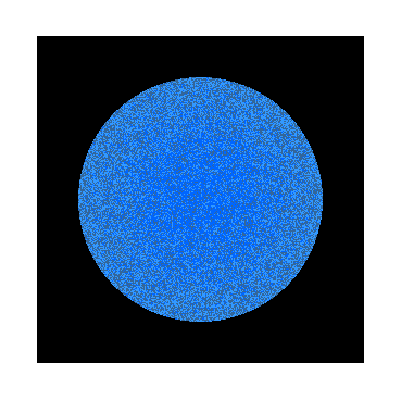

```mathematica
CreateAtmosphere[300,{RGBColor[0.2, 0.6, 1.],RGBColor[0.2, 0.4, 0.6],RGBColor[0., 0.4, 1.]},{2,2,1}]
```

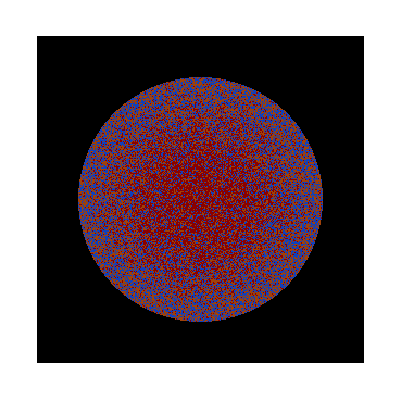

```mathematica
CreateAtmosphere[300,Map[Setting,{0.6235294117647059,0.06666666666666667,0.5411764705882353}],{2,2,1}]
```

Capa de continentes

```mathematica
amplitude=0.5;
frequency=1.0;
gain=0.5;
lacunarity=2.0;
increment=7.0;
scale=35.0;
CreateContinents[size_,pixelSize_,colorGradient_:ColorData["DarkTerrain"]]:=Module[{p,landImg, filter,filterImg},
p = perlin[size,size];
p = Map[colorGradient[Round[#,pixelSize]]&,p,{2}];
Return[ArrayPlot[p,Frame->False]];
];
```

```mathematica
ColorData["CherryTones"]
```

```mathematica
ColorData["SiennaTones"]
```

```mathematica
ColorData["SolarColors"]
```

```mathematica
ColorData["DarkTerrain"]
```

ColorDataFunction[…]

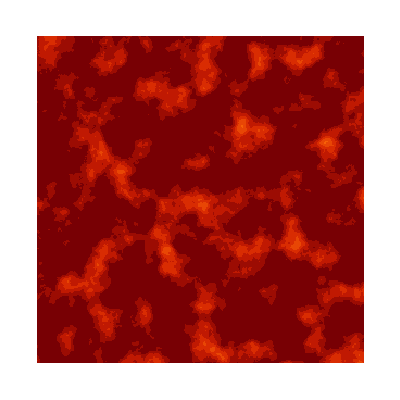

```mathematica
continents = CreateContinents[300,0.1,ColorData["SolarColors"]]
```

```mathematica
roads = SkeletonTransform[ColorNegate[Binarize[continents]]]
```

-Graphics-

```mathematica
ImageAdd[continents,ImageMultiply[roads,0.05]]
```

-Graphics-

Capa de reflejo de luz

```mathematica
CreateSpecularity[size_,r1_,r2_,multiplier_]:=Module[{shade,delta},
delta = 8/size;
shade = Table[
If[Norm[{x,y}]≤3,
RandomChoice[{multiplier*ShadeDist[{x,y},r1,r2],1-multiplier*ShadeDist[{x,y},r1,r2]}->{White,Black}],
Black
],
{x,-4,4,delta},{y,-4,4,delta}
];
Return[ArrayPlot[shade,Frame->False]];
];
```

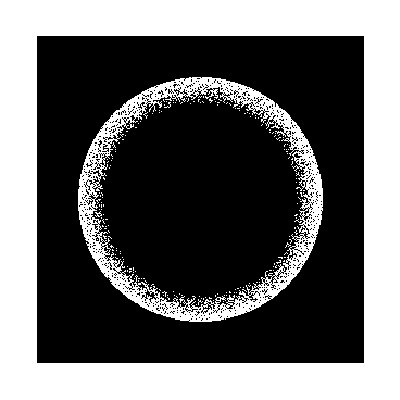

```mathematica
CreateSpecularity[300,1.4,2,200]
```

Capa de filtro circular

```mathematica
CreateCircularFilter[size_]:=Module[{delta,filter},
delta = 8/size;
filter = Table[
If[Norm[{x,y}]≤3,
Black,
White
],
{x,-4,4,delta},{y,-4,4,delta}
];
Return[ArrayPlot[filter,Frame->False]];
];
```

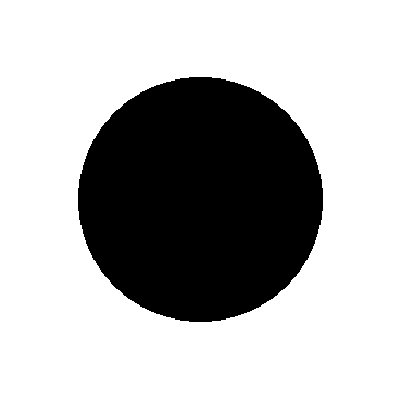

```mathematica
CreateCircularFilter[300]
```

Sombra de planeta

```mathematica
CreatePlanetShade[size_]:=Module[{delta,filter},
delta = 8/size;
filter = Table[
If[(Norm[{x,y}]≤3) && (Norm[{x-3,y}]≤4),
Black,
White
],
{x,-4,4,delta},{y,-4,4,delta}
];
Return[ArrayPlot[filter,Frame->False]];
];
```

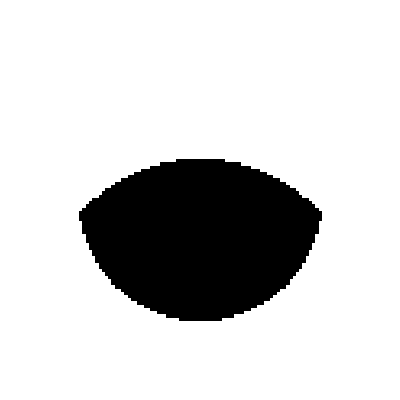

```mathematica
CreatePlanetShade[100]
```

Deformación de imágenes

```mathematica
SpherizeTransform[s_,pt_,exponent_]:=Module[{r=Norm[pt-s]^exponent/Norm[s],a= Apply[ArcTan,pt-s]},(s+r{Cos[a],Sin[a]})];
SpherizeImage[img_,intensity_:1.5]:=ImageTransformation[img,SpherizeTransform[{0.5,0.5},#,intensity]&];
ShiftImage[img_,phase_]:=ImageTransformation[img,{FractionalPart[First[#]+phase],Last[#]}&];
```

Resultado final

```mathematica
world = CreateContinents[150,0.1,ColorData["SolarColors"]];
circularFilter = CreateCircularFilter[150];
shade = CreateSpecularity[150,1.4,2,200];
```

```mathematica
roads = SkeletonTransform[ColorNegate[Binarize[world]]];
world2 = ImageAdd[world,ImageMultiply[roads,0.05]];
sphericalLand = SpherizeImage[world2];
circularSphericalLand = ImageSubtract[sphericalLand,circularFilter];
```

```mathematica
atmosphere = CreateAtmosphere[170,Map[Setting,{0.6235294117647059,0.06666666666666667,0.5411764705882353}],{2,2,1}];
```

```mathematica
planetShade = CreatePlanetShade[150];
```

```mathematica
ImageAdd[circularSphericalLand,ImageMultiply[atmosphere,0.4]]
```

-Graphics-

```mathematica
ImageAdd[ImageMultiply[ImageAdd[circularSphericalLand,atmosphere],ImageAdd[planetShade,0.3]],ImageMultiply[shade,0.1]]
```

-Graphics-

Tierra rotando

```mathematica
world = CreateContinents[150,0.1];
roads = SkeletonTransform[ColorNegate[Binarize[world]]];
world2 = ImageAdd[world,ImageMultiply[roads,0.05]];

circularFilter = CreateCircularFilter[150];
shade = CreateSpecularity[150,1.4,2,200];
planetShade = CreatePlanetShade[150];

earths = ParallelTable[
sphericalLand = SpherizeImage[ShiftImage[world,phase]];
circularSphericalLand = ImageSubtract[sphericalLand,circularFilter];
atmosphere = CreateAtmosphere[170,{RGBColor[0.2, 0.6, 1.],RGBColor[0.2, 0.4, 0.6],RGBColor[0., 0.4, 1.]},{2,2,1}];
ImageAdd[ImageMultiply[ImageAdd[circularSphericalLand,atmosphere],ImageAdd[planetShade,0.3]],ImageMultiply[shade,0.1]]
,{phase,0,0.35,0.015}
];
```

```mathematica
Manipulate[earths[[i]],{i,1,Length[earths],1}]
```

Exportar imágenes

```mathematica
ExportImages[file_,frames_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[Length[frames]]];
directory = DirectoryName[file];
name = FileBaseName[file];

MapIndexed[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[#2,10,indexLength],".png"]}],
#1
]&,
frames
]
];
```

```mathematica
ExportImages[FileNameJoin[{NotebookDirectory[],"good_earth","image.png"}],earths];
```

## Universo

v1

Source: George Varnavides: “An SE Legacy Re-imagined as a Self-Triggering Dynamic”
Link to original: http://blog.wolfram.com/2016/11/09/the-2016-wolfram-one-liner-competition-winners/

```mathematica
PointsPlot[points_]:=
Binarize@Rasterize[
Graphics3D[
{White,PointSize[0.01],Point[points]},
Boxed->False,
Background->GrayLevel[0],
ImageSize->400,
SphericalRegion->True,
ImagePadding->20
]
];

{v,p}=RandomPoint[Ball[],#]&/@{1500,15000};
n=Nearest[v];
f[x_,y_]:=0.9975 (x+0.01 (x-y));
```

```mathematica
pointsEvolution = NestList[f[#,First/@n/@#]&,p,1500];
```

```mathematica
frames = Map[PointsPlot,pointsEvolution];
```

```mathematica
Manipulate[Reverse[frames][[i]],{i,1,Length[frames],1}]
```

```mathematica
ExportImages[FileNameJoin[{NotebookDirectory[],"universe","universe.png"}],Reverse[frames]];
```

v2

```mathematica
Enneper[u_,v_,θ_]:=Module[{z},Re[E^(I θ) {z-z^3/3,I z+I z^3/3,z^2}/.z->u+I v]]

frames = Table[
Binarize@Rasterize@Graphics3D[
{
White,
Thickness[.003],
Line[Table[Enneper[u,v,θ],{u,-3/2,3/2,1/5},{v,-3/2,3/2,1/20}]],
Line[Table[Enneper[u,v,θ+Pi],{v,-3/2,3/2,1/5},{u,-3/2,3/2,1/20}]]},
PlotRange->4.5,
ViewPoint->Top,
Boxed->False,
Axes->None,
Background->Black,
ImageSize->500,
ViewAngle->.47]
,
{θ,0,2 π,0.1}
];
```

```mathematica
Manipulate[frames[[i]],{i,1,Length[frames],1}]
```

```mathematica
ExportImages[FileNameJoin[{NotebookDirectory[],"universe2","universe.png"}],frames];
```

## Ondas

Author: Simon Woods
Link: https://community.wolfram.com/groups/-/m/t/123945

```mathematica
a=RandomReal[1,500 {1,1}];Dynamic[Binarize[Image[a=Rescale[a-GradientFilter[a,2,Method->"Sobel"]]],0.7]]
```

```mathematica
a=RandomReal[1,500 {1,1}];
tbl = Table[
a = Rescale[a-GradientFilter[a,2,Method->"Sobel"]];
Binarize[Image[a],0.7],
1000
];
```

```mathematica
Manipulate[tbl[[i]],{i,1,Length[tbl],1}]
```

```mathematica
a=CrossMatrix[10,200];
Dynamic[Image[a=Rescale[Round[a-GradientFilter[a,2,Method->"Sobel"],0.09]]]]
```

Author: Vitaliy Kaurov
Link: https://community.wolfram.com/groups/-/m/t/123945

```mathematica
a=RandomReal[1,200 {1,1}];
Manipulate[Image[a=Rescale[a-GradientFilter[a,2]-s a^p]],{{p,1.3},.01,2},{{s,.9},0,2}]
```

## Estela de un cometa

```mathematica
triangle = Triangle[{{0,0},{-1,1.5},{10,10}}];
cometa = Table[Image[Graphics[{PointSize[Tiny],White,Point[RandomPoint[triangle,50]]},ImageSize->55,Background->Black]],200];
Manipulate[cometa[[i]],{i,1,Length[cometa],1}]
```

## Patrones repetitivos (para bosque)

Coordenadas del patrón

```mathematica
PolarCoordinate[r_,t_]:=(r {Cos[t],Sin[t]}+1)/2;
SpiralCoordinates[n_,interval_:1]:=Module[{g,coord},
g=2 Pi (1-1/GoldenRatio);
coord = Table[N[PolarCoordinate[Sqrt[i/n],i g]],{i,1,n,interval}];
Return[coord];
];
```

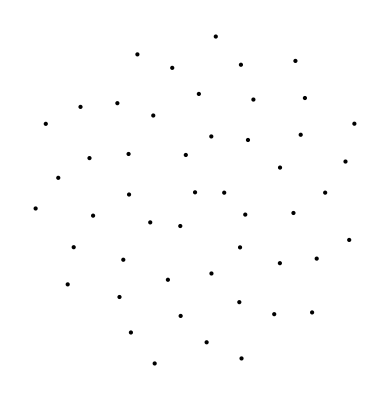

```mathematica
Graphics[Point[SpiralCoordinates[1000,20]]]
```

Aplicación a textura

```mathematica
TexturePattern[img_,canvasSize_,n_,interval_:20]:=Module[{canvas,sortedCoord,result},
canvas = ConstantImage[Transparent,canvasSize];
sortedCoord = Reverse[SortBy[SpiralCoordinates[1000,interval],Last]];
result = Fold[ImageCompose[#1,ImageResize[img,Scaled[1-Last[#2]]],Scaled[{1,0.3}*#2+{0,0.3}]]&,canvas,sortedCoord];
Return[result];
];
```

```mathematica
img = -Graphics-;
TexturePattern[img,{500,300},1000]
```

-Graphics-

## Simulación de galaxia

Basado en: http://demonstrations.wolfram.com/CollidingGalaxies/

```mathematica
m1=5;
minRad=5;

Norms[{x_,0|0.,0|0.}]:={{0,1,0},{0,0,1}};
Norms[v_List]:=Module[{w,u,wy,wz,ux,uy,uz},
w={0,wy,wz};
u={ux,uy,uz};
w=w/.First[NSolve[{w.v==0,w.w==1},{wy,wz}]];
u=u/.First[NSolve[{u.v==0,u.w==0,u.u==1},u]];
Return[{w,u}];
];

PosAndVel[{a_,b_,c_},{r_,dr_},m_]:=Module[{xp,yp,pos,unitvel,vel,xandy},
{xp,yp}=Norms[{a,b,c}];
xandy=Select[Flatten[Table[{x,y},{x,-r,r,dr},{y,-r,r,dr}],1],(minRad^2<(#.#)<r^2)&];
pos=Map[(xp #[[1]]+yp #[[2]])&,xandy];
unitvel=Map[((-#[[1]] yp+#[[2]] xp)/Sqrt[#[[1]]^2+#[[2]]^2])&,xandy];
vel=Map[#[[1]]*Sqrt[m/Sqrt[#[[2]].#[[2]]]]&,Transpose[{unitvel,pos}]];
Return[{pos,vel}];
];

CenterOfMass[{X1_,Y1_,Z1_},{X2_,Y2_,Z2_},{M1_,M2_}]:={(M1 X1+M2 X2)/(M1+M2),(M1 Y1+M2 Y2)/(M1+M2),(M1 Z1+M2 Z2)/(M1+M2)};

Realign[XX1_,XX2_,M2_,pos_,pos2_]:=Module[{cm,poslocal,pos2local,XX1local,XX2local},
cm=CenterOfMass[XX1,XX2,{m1,M2}];
poslocal=Map[#-cm&,pos];
pos2local=Map[#-cm&,pos2];
XX1local=XX1-cm;
XX2local=XX2-cm;
Return[{M2,poslocal,pos2local,XX1local,XX2local}];
];

Init[Dist_,MF_,XX1_,XX2_,pos_,pos2_,vel_,vel2_,V1_,V2_,ss_,tcol_,icol_,vp_,TIME_,ir_,tr_,sep_]:=Module[{Rad1,Rad2,dr,intpl,Distlocal,MFlocal,M2local,poslocal,pos2local,vellocal,vel2local,XX1local,XX2local,V1local,V2local,sslocal,tcollocal,icollocal,vplocal,TIMElocal},
{Distlocal,Rad1,Rad2,dr,MFlocal,XX2local,V2local,intpl,sslocal,tcollocal,icollocal,vplocal,TIMElocal}={100,tr,ir,sep,MF,XX2,V2,Automatic,.001,Green,Cyan,{1.3,-2.4,2.},0};
intpl=V2local;
(*If[intpl===Automatic,intpl=V2local];*)
XX1local=V1local={0.,0.,0.};
M2local=MFlocal * m1;
{poslocal,vellocal}=PosAndVel[{0,0,1},{Rad1,dr},m1];
{pos2local,vel2local}=PosAndVel[intpl,{Rad2,dr},M2local];
pos2local=Map[(#+XX2)&,pos2local];
vel2local=Map[(#+V2)&,vel2local];
Return[{Distlocal,MFlocal,V1local,V2local,sslocal,tcollocal,icollocal,vplocal,TIMElocal,Sequence@@Realign[XX1local,XX2local,M2local,poslocal,pos2local],vellocal,vel2local}];
];

(* Find the updated positions, velocities, and accelerations for all particles. *)
NewStars[pos_,vel_,XX1_,XX2_,M1_,M2_]:=Module[{r1,r2,a1,a2,acc,newpos,newvel,delpos},
delpos=Position[pos,XX1|XX2];
newpos=Delete[pos,delpos];
newvel=Delete[vel,delpos];
r1=Map[(#-XX1)&,newpos];
r2=Map[(#-XX2)&,newpos];
a1=-Map[M1/Dot[#,#]^(3/2)*#&,r1];
a2=-Map[M2/Dot[#,#]^(3/2)*#&,r2];
acc=a1+a2;
newpos=newpos+newvel+acc/2;
newvel=newvel+acc;
Return[{newpos,newvel}];
];

(* Iterate the simulation by one time step per call, assuming Keplerian orbits about the galaxy centers. *)
Iterate[XX1_,XX2_,M2_,pos_,pos2_,vel_,vel2_,V1_,V2_,TIME_]:=Module[{a1,a2,acc,rr,ar1,ar2,poslocal,vellocal,pos2local,vel2local,XX1local,XX2local,V1local,V2local,TIMElocal},
(* starts in target galaxy *)
{poslocal,vellocal}=NewStars[pos,vel,XX1,XX2,m1,M2];
(* starts in intruder galaxy *)
{pos2local,vel2local}=NewStars[pos2,vel2,XX1,XX2,m1,M2];
(* two galaxies *)
rr=XX2-XX1;
ar1=M2*rr/(rr.rr)^(3/2);
ar2=-m1*rr/(rr.rr)^(3/2);
XX1local=XX1+V1+ar1/2;
XX2local=XX2+V2+ar2/2;
V1local=V1+ar1;
V2local=V2+ar2;
TIMElocal=TIME+1;
Return[{poslocal,pos2local,vellocal,vel2local,XX1local,XX2local,V1local,V2local,TIMElocal}];
];
```

Valores iniciales e inicialización

```mathematica
tr = 60; ir = 20;
sep = 4;
step = 50;
MF = 0.1;

iposx = -50; iposy = 50; iposz = 50;
ivelx = 0; ively = -0.33; ivelz = -0.33;

Dist = 100;
V1 = {0,0,0}; V2 = {1,0,0};
ss = 0.001;
tcol = Green; icol = Cyan;
XX1 = {0,0,0};
pos2 = {-50,50,50};
vel = {0,0,0};
vp = {1.3,-2.4,2.};
TIME = 0;
{Dist,MF,V1,V2,ss,tcol,icol,vp,TIME,M2,pos,pos2,XX1,XX2,vel,vel2}=Init[Dist,MF,XX1,{iposx,iposy,iposz},{iposx,iposy,iposz},pos2,vel,{ivelx,ively,ivelz},V1,{ivelx,ively,ivelz},ss,tcol,icol,vp,TIME,ir,tr,sep];
```

Funciones estéticas

```mathematica
GalaxyPoints[pos_,pointSize_,colorFunction_]:=Module[{distances,colors,points},
distances = Map[Norm[#-XX1]&,pos];
colors = Map[colorFunction[RandomReal[{0,1}]]&,distances];
points = Map[Point,pos];
Return[Transpose[{colors,ConstantArray[PointSize[pointSize],Length[pos]],points}]];

];
GalaxyCore[region_,number_,pointSize_,opacity_,colors_]:=Module[{points,pointColors},
points = Map[Point,RandomPoint[region,number]];
pointColors = Table[RandomChoice[colors],number];
Return[Transpose[{pointColors,ConstantArray[opacity,number],ConstantArray[pointSize,number],points}]];
];

Draw[XX1_,XX2_,MF_,pos_,pos2_,Dist_,TIME_,vp_,ss_,tcol_,icol_]:=Module[{cm=CenterOfMass[XX1,XX2,{m1,m1*MF}]},
Graphics3D[
{
GalaxyPoints[pos,0.006,Blend[{RGBColor[0.5086566, 0.7417834000000001, 0.9630335999999999],RGBColor[0.9336260000000001, 0.7795129999999999, 0.44584699999999994]},#]&],GalaxyPoints[pos2,ss,Blend[{LightBlue,LightRed},#]&],
GalaxyCore[Ellipsoid[XX1,10*{2,2,1}], 1500,PointSize[0.006],Opacity[0.6],{RGBColor[0.8051914000000001, 0.9672204, 0.98804],RGBColor[0.931655, 0.9952084999999999, 0.9090485],RGBColor[0.9906662, 0.99486515, 0.83423735]}],GalaxyCore[Ellipsoid[XX2,3*{2,2,1}], 200,PointSize[0.006],Opacity[0.6],{RGBColor[0.8051914000000001, 0.9672204, 0.98804],RGBColor[0.931655, 0.9952084999999999, 0.9090485],RGBColor[0.9906662, 0.99486515, 0.83423735]}]
},
PlotRange->{{-Dist+cm[[1]],Dist+cm[[1]]},{-Dist+cm[[2]],Dist+cm[[2]]},{-Dist+cm[[3]],Dist+cm[[3]]}},
Boxed->False,
ViewPoint->vp,
Background->GrayLevel[0],
ImageSize->400,
SphericalRegion->True,
ImagePadding->20
]
];
```

```mathematica
Binarize@Rasterize@Draw[XX1,XX2,MF,pos,pos2,Dist,TIME,vp,.005,tcol,icol]
```

-Graphics-

Simulación

```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
imgs = {};
ProgressDo[
{pos,pos2,vel,vel2,XX1,XX2,V1,V2,TIME}=Iterate[XX1,XX2,M2,pos,pos2,vel,vel2,V1,V2,TIME];
AppendTo[imgs,Binarize[Rasterize[Draw[XX1,XX2,MF,pos,pos2,Dist,TIME,vp,.005,tcol,icol]]]];
,1500
];
```

$Aborted

```mathematica
Manipulate[imgs[[i]],{i,1,Length[imgs],1}]
```

Exportar

```mathematica
FileNamingFunction[file_,index_,totalSize_]:=Block[{directory,name},
directory = DirectoryName[file];
name = FileBaseName[file];
FileNameJoin[{directory,StringJoin[name,IntegerString[index,10,Length[IntegerDigits[totalSize]]],".png"]}]
];
```

```mathematica
Block[{i},
ProgressDo[
{pos,pos2,vel,vel2,XX1,XX2,V1,V2,TIME}=Iterate[XX1,XX2,M2,pos,pos2,vel,vel2,V1,V2,TIME];

Export[
FileNamingFunction[FileNameJoin[{NotebookDirectory[],"galaxy","galaxy.png"}],i,1500],
Binarize[Rasterize[Draw[XX1,XX2,MF,pos,pos2,Dist,TIME,vp,.005,tcol,icol]]]
];
,{i,1500}
]
]
```

$Aborted

## Edificios

```mathematica
topImage = Import[FileNameJoin[{NotebookDirectory[],"images","top.png"}]];
centerImage = Import[FileNameJoin[{NotebookDirectory[],"images","center.png"}]];
```

```mathematica
SimpleBuilding[center_Image,top_Image,height_Integer]:=Block[{base},
base = ImageAssemble[Transpose[{ConstantArray[center,height]}]];
ImageAssemble[{{top},{base}}]
];

CompositeBuilding[centerImages_List,top_Image,height_Integer]:=Block[{base},
base = ImageAssemble[Transpose[{Flatten[ConstantArray[centerImages,height]]}]];
ImageAssemble[{{top},{base}}]
];
```

```mathematica
building = SimpleBuilding[centerImage,topImage,4]
```

-Graphics-

```mathematica
CompositeBuilding[{centerImage,ImageReflect[centerImage,Left]},topImage,3]
```

-Graphics-